## EELE 582 Optical Design Homework 5 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 1

#### Third-order coma is given by the expression

```mathematica
Wc = W131 H ρ^3 Cos[ϕ];
```

#### The transverse ray aberration is found using the relation

```mathematica
p2c = {ρ-> √(x^2+y^2),ϕ-> ArcTan[y,x]};
c2p =  {x-> ρ Sin[ϕ],y-> ρ Cos[ϕ]} ;
T[W_]:= -(R/(n r))Grad[(W /. p2c),{x,y}] /. c2p //FullSimplify
```

#### Plug our expression for coma into the transverse ray aberration function

```mathematica
(Tc[ρ_,ϕ_] = T[Wc]) //Framed
```

{-(2 H R W131 ρ^2 Cos[ϕ] Sin[ϕ])/(n r),-(H R W131 ρ^2 (2+Cos[2 ϕ]))/(n r)}

#### Create list of pupil points in polar coordinates

```mathematica
Pρ = {R,R,R,R,R,R,R,R,a R,a R,a R,a R,0} /. R-> 1 /. a->0.7;
Pϕ={0π/4,1π/4,2π/4,3π/4,4π/4,-3π/4,-2π/4,-π/4,π/4,3π/4,-3π/4,-π/4,0};
```

#### Create function to convert from polar to Cartesian coordinates

```mathematica
FromPolar[ρ_,ϕ_]:={ρ Sin[ϕ],ρ Cos[ϕ]}
```

#### Create function to label ray fan plots

```mathematica
chars={"A","B","C","D","E","F","G","H","I","J","K","L","M"};
positions={Top,Right,Right,Right,Bottom,Left,Left,Left,Right,Right,Left,Left, Top};
LabeledListPlot[pts_,k_] := ListPlot[Thread[Labeled[pts,chars,positions]],PlotStyle->PointSize[Large],AspectRatio->1/k]
```

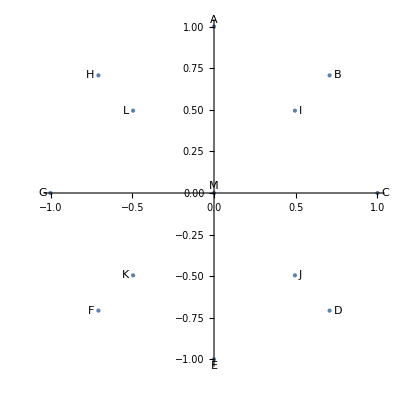

```mathematica
pts=FromPolar[Pρ,Pϕ];
LabeledListPlot[Transpose[pts],1]
```

#### Evaluate our expression for 3rd-order coma at each point in the pupil

{{0,-1,0,1,0,-1,0,1,-0.49,0.49,-0.49,0.49,0},{-3,-2,-1,-2,-3,-2,-1,-2,-0.98,-0.98,-0.98,-0.98,0}}

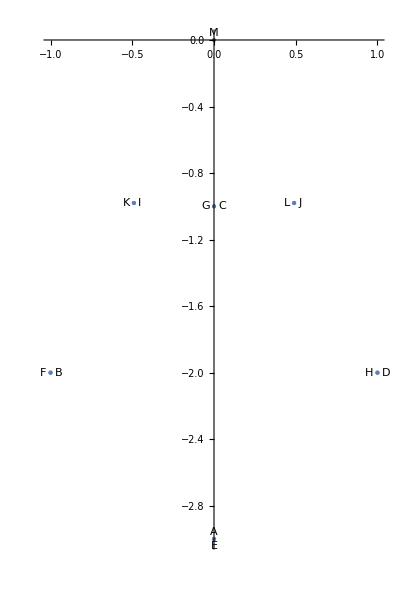

```mathematica
pts=Tc[Pρ,Pϕ] /. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1, a-> 0.7}
LabeledListPlot[Transpose[pts],2/3]
```

## Problem 2

#### Enter in the expression for defocus wavefront aberration

```mathematica
Wdf = W020 ρ^2;
```

#### Find the defocus transverse ray aberration

```mathematica
Tdf[ρ_,ϕ_] = T[Wdf]
```

{-(2 R W020 ρ Sin[ϕ])/(n r),-(2 R W020 ρ Cos[ϕ])/(n r)}

### Part a

#### Enter the expression for spherical wavefront aberration

```mathematica
Ws = W040 ρ^4;
```

#### Find the spherical transverse ray aberration

```mathematica
Ts[ρ_,ϕ_] = T[Ws]
```

{-(4 R W040 ρ^3 Sin[ϕ])/(n r),-(4 R W040 ρ^3 Cos[ϕ])/(n r)}

#### Solve for where the sum of the spherical and defocus transverse ray aberration is zero

```mathematica
TpA[ρ_,ϕ_] = Tdf[ρ,ϕ] + Ts[ρ,ϕ];
```

```mathematica
SpA = Solve[Part[TpA[0.7,0],2] == 0, W020]
```

{{W020→-0.98 W040}}

#### Plot the spot diagram

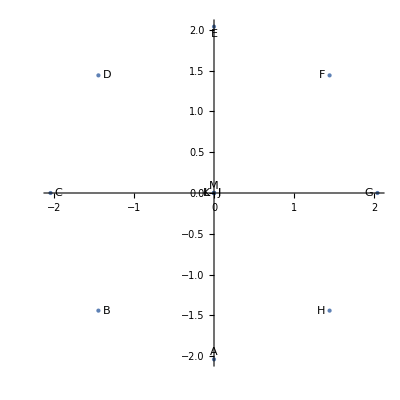

```mathematica
pts=TpA[Pρ,Pϕ] /. SpA[[1]] /. {H -> 1, R-> 1, W040-> 1,r->1, n-> 1, a-> 0.7};
LabeledListPlot[Transpose[pts],1]
```

#### Plot the ray fan

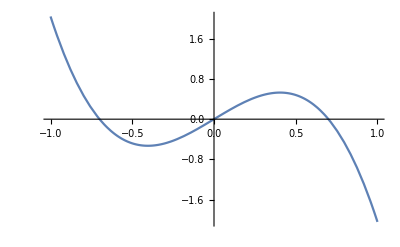

```mathematica
EpA=TpA[ρ,ϕ] /. p2c /. x->0 /. SpA[[1]] /. {H -> 1, R-> 1, W040-> 1,r->1, n-> 1, a-> 0.7};
Plot[EpA[[2]], {y,-1,1}]
```

### Part b.

#### Enter the expression for astigmatic wavefront aberration

```mathematica
Wa = W222 H^2 ρ^2 Cos[ϕ]^2;
```

#### Find the astigmatic transverse ray aberration

```mathematica
Ta[ρ_,ϕ_] = T[Wa]
```

{0,-(2 H^2 R W222 ρ Cos[ϕ])/(n r)}

#### Solve for where the sum of the spherical and defocus transverse ray aberration is zero

```mathematica
TpB[ρ_,ϕ_] = Tdf[ρ,ϕ] + Ta[ρ,ϕ];
```

```mathematica
SpB = Solve[Part[TpB[1,0],2] == Part[TpB[1,-π/2],1], W020]
```

{{W020→-(H^2 W222)/2}}

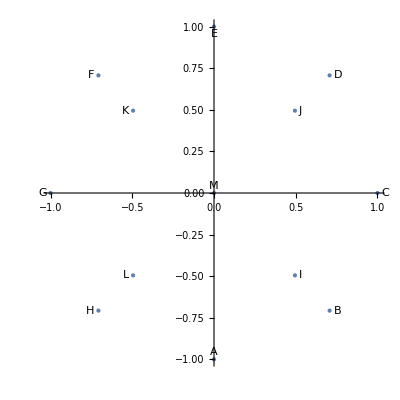

```mathematica
pts=TpB[Pρ,Pϕ]/.SpB[[1]] /. {H -> 1, R-> 1, W222-> 1,r->1, n-> 1, a-> 0.7};
LabeledListPlot[Transpose[pts],1]
```

#### Plot the ray fan

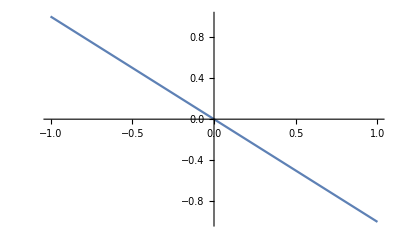

```mathematica
EpB=TpB[ρ,ϕ] /. p2c /. x->0 /. SpB[[1]] /. {H -> 1, R-> 1, W222-> 1,r->1, n-> 1, a-> 0.7};
Plot[EpB[[2]], {y,-1,1}]
```

### Part c.

#### Since we already calculated the expression for coma in part a, just solve for where the marginal ray is zero

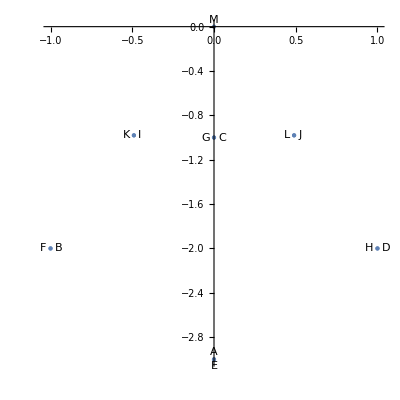

```mathematica
pts=Tc[Pρ,Pϕ] /. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1, a-> 0.7};
LabeledListPlot[Transpose[pts],1]
```

#### Plot the ray fan

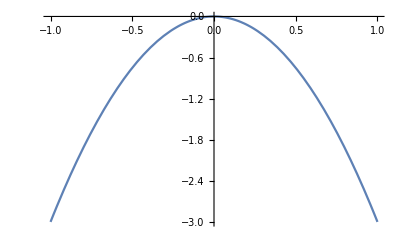

```mathematica
EpC=Tc[ρ,ϕ] /. p2c /. x->0  /. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1, a-> 0.7};
Plot[EpC[[2]], {y,-1,1}] //Quiet
```

### Part d.

#### Enter the expression for distortion wavefront aberration

```mathematica
Wdi = W311 H^3 ρ Cos[ϕ];
```

#### Find the distortion transverse ray aberration

```mathematica
Tdi[ρ_,ϕ_] = T[Wdi]
```

{0,-(H^3 R W311)/(n r)}

#### Add the defocus term

```mathematica
TpD[ρ_,ϕ_] = Tdf[ρ,ϕ] + Tdi[ρ,ϕ]
```

{-(2 R W020 ρ Sin[ϕ])/(n r),-(H^3 R W311)/(n r)-(2 R W020 ρ Cos[ϕ])/(n r)}

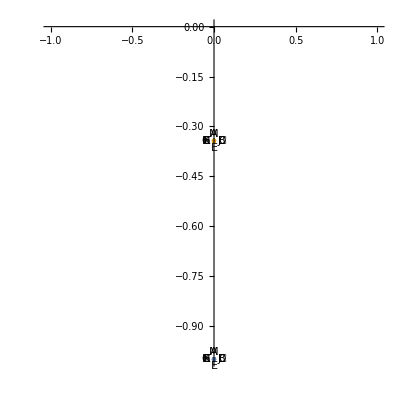

```mathematica
pts1=TpD[Pρ,Pϕ] /. W020->0/. {H -> 1, R-> 1, W311-> 1,r->1, n-> 1, a-> 0.7};
pts2 = TpD[Pρ,Pϕ] /.  W020->0/. {H -> 0.7, R-> 1, W311-> 1,r->1, n-> 1, a-> 0.7};
ListPlot[{Thread[Labeled[Transpose[pts1],chars,positions]],Thread[Labeled[Transpose[pts2],chars,positions]]},PlotStyle->PointSize[Large],AspectRatio->1]
```

#### Plot the ray fan

{{0,-1},{0,-0.343}}

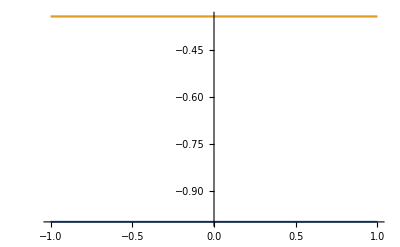

```mathematica
EpD={TpD[ρ,ϕ] /. p2c /. x->0 /. W020->0 /. {H -> 1, R-> 1, W311-> 1,r->1, n-> 1, a-> 0.7},TpD[ρ,ϕ] /. p2c /. x->0 /. W020->0 /. {H -> 0.7, R-> 1, W311-> 1,r->1, n-> 1, a-> 0.7}}
Plot[{EpD[[1,2]],EpD[[2,2]]}, {y,-1,1}]
```

## Problem 3

### Part a.

#### Use triangles to find the aberrations in the paraxial plane

```mathematica
vals3 = {LRA3a1->-1.0 Quantity[, "Micrometers"]  ,LRA3a2-> -0.5 Quantity[, "Micrometers"],tanU3a1->-0.05,tanU3a2->-0.035};
```

```mathematica
(TRA3a1 = -LRA3a1 tanU3a1 /. vals3) //Framed
```

-0.05 µm

```mathematica
(TRA3a2 = -LRA3a2 tanU3a2 /. vals3) //Framed
```

-0.0175 µm

### Part b.

```mathematica
Δz = -0.2 Quantity[, "Micrometers"];
```

```mathematica
(TRA3a1 = -(LRA3a1-Δz) tanU3a1 /. vals3) //Framed
```

-0.04 µm

```mathematica
(TRA3a2 = -(LRA3a2-Δz) tanU3a2 /. vals3) //Framed
```

-0.0105 µm

## Problem 4

#### Summary

From the plots below we can see that the Zernike polynomials are simply a linear combination of the Siedel polynomials in Cartesian coordinates. The relationship of the naming convention appears to be based off comparing the leading term of the Zernikes to the corresponding Siedel aberration.

#### Spherical

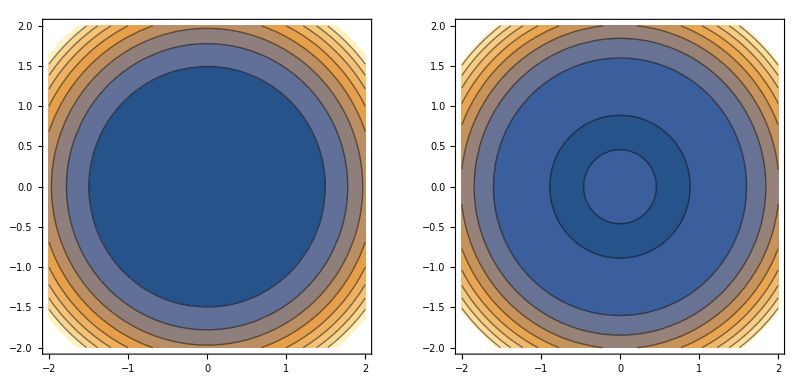

(x^2+y^2)^2

1-6 (x^2+y^2)+6 (x^2+y^2)^2

```mathematica
Zps = 6 ρ^4-6 ρ^2+1;
a1=ContourPlot[Ws /. p2c/. {H -> 1, R-> 1, W040-> 1,r->1, n-> 1}, {x,-2,2},{y,-2,2}];
a2=ContourPlot[Zps /. p2c, {x,-2,2},{y,-2,2}];
GraphicsGrid[{{a1,a2}}]
Ws /. p2c/. {H -> 1, R-> 1, W040-> 1,r->1, n-> 1} //FullSimplify
Zps /. p2c//FullSimplify
```

#### Astigmatism

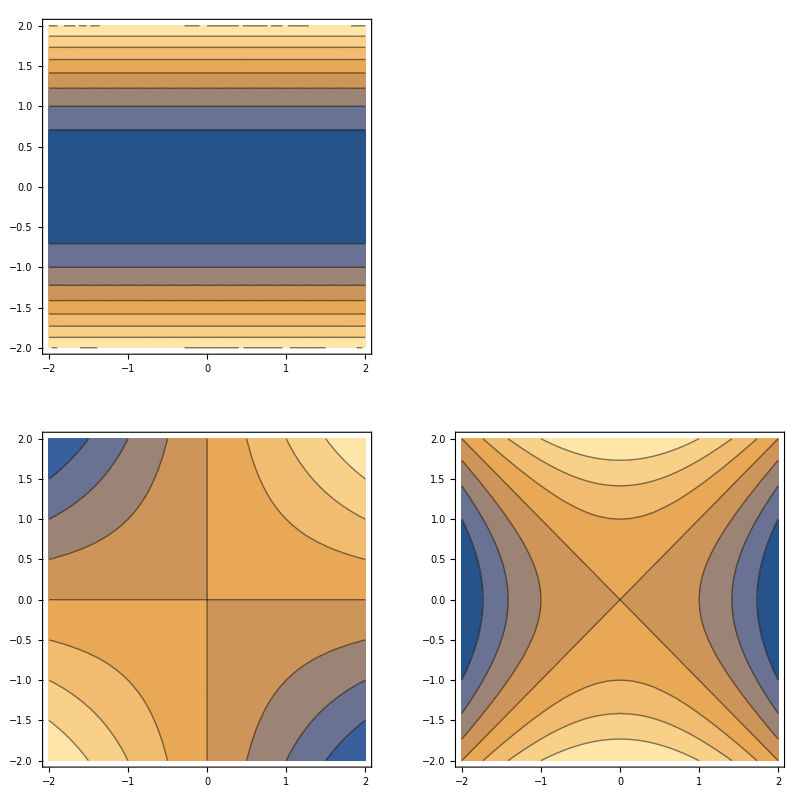

```mathematica
Zoa = ρ^2 Sin[2ϕ];
Zva = ρ^2 Cos[2ϕ];
a1=ContourPlot[Wa /. p2c/. {H -> 1, R-> 1, W222-> 1,r->1, n-> 1}, {x,-2,2},{y,-2,2}];
a2=ContourPlot[Zoa /. p2c, {x,-2,2},{y,-2,2}];
a3=ContourPlot[Zva /. p2c, {x,-2,2},{y,-2,2}];
GraphicsGrid[{{a1},{a2,a3}}]
```

```mathematica
Wa /. p2c/. {H -> 1, R-> 1, W222-> 1,r->1, n-> 1}
Zoa /. p2c //FullSimplify
Zva /. p2c //FullSimplify
```

y^2

2 x y

-x^2+y^2

#### Coma

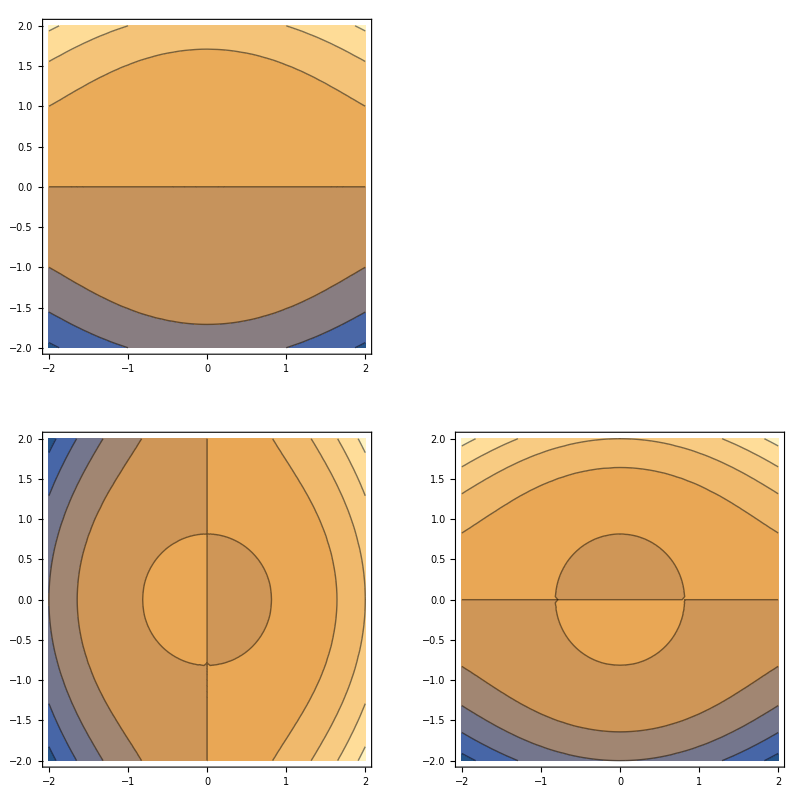

y (x^2+y^2)

x (-2+3 x^2+3 y^2)

y (-2+3 x^2+3 y^2)

```mathematica
Zvc =(3 ρ^3-2ρ)Sin[ϕ];
Zhc =(3 ρ^3-2ρ)Cos[ϕ];
a1=ContourPlot[Wc /. p2c/. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1}, {x,-2,2},{y,-2,2}];
a2=ContourPlot[Zvc /. p2c, {x,-2,2},{y,-2,2}];
a3=ContourPlot[Zhc /. p2c, {x,-2,2},{y,-2,2}];
GraphicsGrid[{{a1},{a2,a3}}]
Wc /. p2c/. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1}
Zvc /. p2c //FullSimplify
Zhc /. p2c //FullSimplify
```